```mathematica
Remove[BB, CC]
aa := 1
dd := 1
rA := 2
```

```mathematica
psi1[x_] := Exp[- I * k * x] - Exp[I * k * x]
psi2[x_] := BB * Exp[-I * k * x] + CC * Exp[I * k * x]
```

```mathematica
Solve[{
psi1[dd] == psi2[dd],
psi2'[dd] - psi1'[dd] == - aa * psi1[dd]
}, {BB, CC}]
```

{{BB→(ⅈ (-1+ⅇ^(2 ⅈ k)-2 ⅈ k))/(2 k),CC→-(ⅇ^(-2 ⅈ k) (-ⅈ+ⅈ ⅇ^(2 ⅈ k)+2 ⅇ^(2 ⅈ k) k))/(2 k)}}

```mathematica
BB = (ⅈ (-1+ⅇ^(2 ⅈ k)-2 ⅈ k))/(2 k)
CC=-(ⅇ^(-2 ⅈ k) (-ⅈ+ⅈ ⅇ^(2 ⅈ k)+2 ⅇ^(2 ⅈ k) k))/(2 k)
```

(ⅈ (-1+ⅇ^(2 ⅈ k)-2 ⅈ k))/(2 k)

-(ⅇ^(-2 ⅈ k) (-ⅈ+ⅈ ⅇ^(2 ⅈ k)+2 ⅇ^(2 ⅈ k) k))/(2 k)

```mathematica
eq = FullSimplify[rA * psi2'[rA] / psi2[rA]]
```

(2 k (-k+Cot[k] (-1+k Cot[k])))/(-1+2 k Cot[k])

```mathematica
Limit[eq,k->0]
```

0

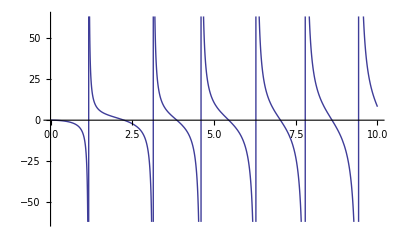

```mathematica
Plot[eq,{k,0.0,10.0}]
```

So, for each B < 0 we have extra state